# Differential Equations for High School Students

Kyungwon Chun
ruddyscent@gmail.com
BioBrain Inc.

```mathematica
DateString[]
$Version
<<SymbolicComputing`
$SCVersion
```

Mon 29 Apr 2019 14:13:53

11.3.0 for Mac OS X x86 (64-bit) (March 7, 2018)

5.0.4 (August 5, 2018)

## Reference

W. E. Boyce and R. C. DiPrima, Elementary Differential Equations and Boundary Value Problems, 10th ed. Wiley, 2012.

-Graphics-
William E. Boyce

## 0 MathSymbolica

## Overview

Mathematica add-on package that facilitates symbolic computation with mathematical expressions

Over 850 functions and own programming language

Display and interpretation of various mathematical expressions like derivatives, integrals, sums, vector operators, brakets, etc. using the traditional notation

## Author

-Graphics-

Ph.D Youngjoo Chung
Professor
School of Information and Communications
Gwangju Institute of Science and Technology (GIST), South Korea
E-mail: ychung@gist.ac.kr

## Keywords

Notation,
Manipulation and
Evaluation
of Mathematical Expressions

## Motivation

To design and implement a symbolic computing system based on Mathematica that can manipulate various mathematical expressions using traditional notation and deferred on-demand evaluation

## Objective

To replace hand-written calculation with symbolic computation and software-based automation

## Features

Allows traditional notation for various mathematical expressions

Algebraic manipulation of formulas using symbolic computation

Seamless integration with the computing environment of Mathematica

Powerful platform for streamlined manipulation of mathematical expressions

## Advantages

Close emulation of hand-written calculation

Allows focusing on concepts and principles rather than tedious, boring, time-consuming and error-prone hand-written calculation

Good readability, enhanced speed and accuracy, and minimization of human errors during calculation

Expressions that closely resemble the traditional mathematical style, e.g., subscripts, derivatives and vector operators

## Brief History

2002. 04: Development started as MiscAlgebra Package (MP)

2007. 11: Presented at the First Korean Mathematica Users Conference

2011. 08: Renamed to Symbolic Computing (SC) Package

2011. 10: Presented at Wolfram Technology Conference 2011

2012. 02: Version 1.0 beta release after the lecture at Mathematics Dept of Korea University

2012. 04: Version 2.0 beta

2014. 12: Version 3.0 beta

2015. 10: Version 3.1 beta

2016. 06: Version 4.0 beta

2017. 12: Version 4.1 (commercial release)

2018. 06: Version 5.0 release

## Installation

```mathematica
ToExpression[URLFetch["https://symbcomp.gist.ac.kr/downloads/InstallSymbComp.m"]]
```

## 1 Introduction

## Historical Remarks

Isaac Newton (1642-1727)
-Graphics-

1687: published Philosophiae Naturalis Principia Mathematica
-Graphics-

1705: knighted

1727: burried in Westminster Abbey
-Graphics-

Gottfried Wilhelm Leibniz (1646-1716)
-Graphics-

1684: published the fundamental results of calculus

1691: invented separation of variables

1694: solved the first order linear equations

## Determinism

-Graphics-+-Graphics-=-Graphics-

## 1.1 Some Basic Mathematical Model; Direction Fields

### Example 1: A Falling Object

-Graphics-

The physical law that governs the motin of objects in Newton’s second law expressed by the equation;

```mathematica
F==m a(*eq1.1*)
SCMAF[%,RA,{At[2],a==ⅆv/ⅆt}]
```

F==a m

F==m ⅆv/ⅆt

where m is the mass of th eobject, v is its velocity,  a is its acceleration, and F is the net force exerted on the object, while t denotes time.

```mathematica
F==m g-γ v(*eq1.3*)
SCMAF[%,RA,{At[1],F==m ⅆv/ⅆt},
SCDivEq,{All,m}]
```

F==g m-v γ

m ⅆv/ⅆt==g m-v γ

ⅆv/ⅆt==g-(v γ)/m

where g is the acceleration due to gravity near the earth’s surface, and γ is a drag coefficient.

### Example 2: A Falling Object (continued)

-Graphics-

```mathematica
ⅆv/ⅆt==g-(v γ)/m(*eq1.4*)
SCMAF[%,RA,{At[2],{γ==2,m==10,g==9.8}}]
(*eq1.5*)
```

ⅆv/ⅆt==g-(v γ)/m

ⅆv/ⅆt==9.8-v/5

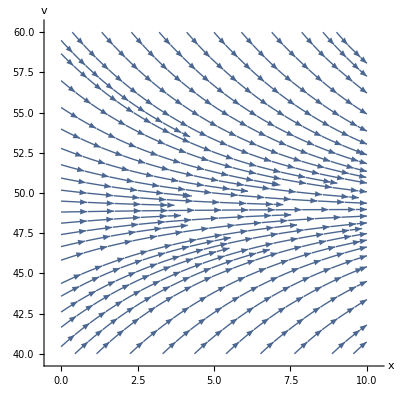

```mathematica
StreamPlot[{1,9.8-v/5},{t,0,10},{v,40,60},Frame->False,Axes->True,AxesLabel->{x,v},AspectRatio->1](*fig1.1.2*)
```

When ⅆv/ⅆt==0, we get an equilibrium solution,

```mathematica
ⅆv/ⅆt==9.8-v/5
SCMAF[%,RA,{At[1],ⅆv/ⅆt==0},
SCSolve,{All,v}]
```

ⅆv/ⅆt==9.8-v/5

0==9.8-v/5

v==49.

This solution is ofen called the terminal velocity.

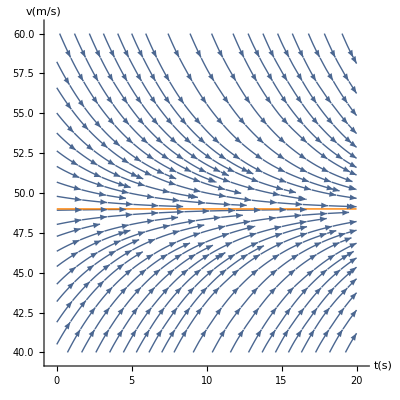

```mathematica
Show[StreamPlot[{1,9.8-v/5},{t,0,20},{v,40,60},Frame->False,Axes->True,AxesLabel->{"t(s)","v(m/s)"},AspectRatio->1],
Plot[49,{t,0,20},PlotStyle->{Orange,Thick}]
](*fig1.1.3*)
```

### Example 3: Field Mice and Owls

-Graphics-

If the mouse population, p(t) increases at a rate proportional to the current population, and 450 field mice per month are killed by owls, the populaiton growth can be expressed by the equation;

ⅆp/ⅆt==-450+0.5 p

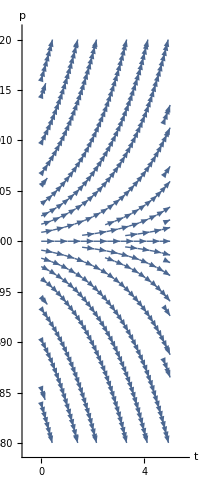

```mathematica
ⅆp/ⅆt==0.5p-450(*eq1.8*)
SCMAF[%,SCApplyFunc,{At[2],StreamPlot[{1,#},{t,0,5},{p,880,920},AxesLabel->{t,p},StreamPoints->Fine,Axes->True,Frame->False,AspectRatio->Full]&},Take->{2}]
```

```mathematica
ⅆp/ⅆt==0.5p-450(*eq1.8*)
SCMAF[%,RA,{At[1],ⅆp/ⅆt==0},
SCSolve,{All,p}]
```

ⅆp/ⅆt==-450+0.5 p

0==-450+0.5 p

p==900.

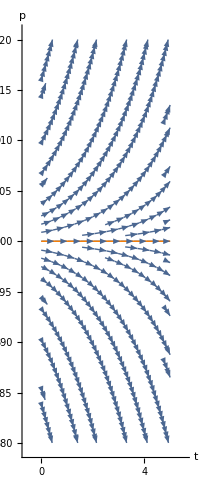

```mathematica
Show[StreamPlot[{1,-450+0.5 p},{t,0,5},{p,880,920},AxesLabel->{t,p},StreamPoints->Fine,Axes->True,Frame->False,AspectRatio->Full],
Plot[900,{t,0,5},PlotStyle->{Orange,Thick}]]
```

### Constructing Mathematical Models

Identify the independnet and dependent variables.

Choose the units of measurement for each variable.

Articularte the basic principle that underlies or governs the problem you are investigating.

Express the principle or law in step 3 in terms of the varibles you choose in step 1.

Make sure that all terms in your equation have the same physical units.